```mathematica
Get[NotebookDirectory[]<>#]&/@
{
"combine_packages.wls",
"load_takahashi_data.wl"
};
```

```mathematica
figureNameGrid="light_temperature_grid";
figureDirectoryGrid=figureNameGrid;
```

```mathematica
tempSelection={25,34,35};
lightsSelection={0,200,2000};
Clear[dataPlot];
dataPlot["MixStress"][temperature_,light_,options_:{}]:=If[ListQ[dat["MixStress"][temperature,light]],ListPlot[dat["MixStress"][temperature,light],Evaluate@options,Joined->False,PlotMarkers->plotMarkers,PlotStyle->{Darker@Gray,Dashed,thickness},imageSizePadding[ImagePaddingXunits],FrameTicks->{{autoTicks,None},{{0}~Join~hourTicks[[1;;-1;;1]],None}},PlotRange->{{-.1,1.05}3.5 3600,{FvFmMinPlot,FvFmMaxPlot}},Evaluate@style],Nothing];
Table[dat["MixStress"][temperature,0]=DeleteDuplicates@Normal@Select[data["FigS1"],#"temp"==temperature&][All,{3600#["h"]&,#["Fv/Fm"]&}],{temperature,tempSelection}];
(*note: temp treat starts at h=-.5, [or at h=0 after shift] (in dark), light at h=0 [1/2 after shift]])*) 
Table[dat["MixStress"][temperature,200]=DeleteDuplicates@Normal@Select[data["Fig2B"],#"temp"==temperature&][All,{3600(1/2+#["h"])&,#["Fv/Fm"]&}],{temperature,tempSelection[[1;;2]]}];
dat["MixStress"][25,2000]=Normal[Select[data["Fig3B"],#"temp"==25∧#"h"<=-.05&][All,{3600(#["h"]+1.5)&,#["Fv/Fm"]&}]];
(*Grid[Table[Column[{{temperature,light},Quiet@dataPlot["MixStress"][temperature,light]}] ,{temperature,tempSelection},{light,lightsSelection}]]*)
```

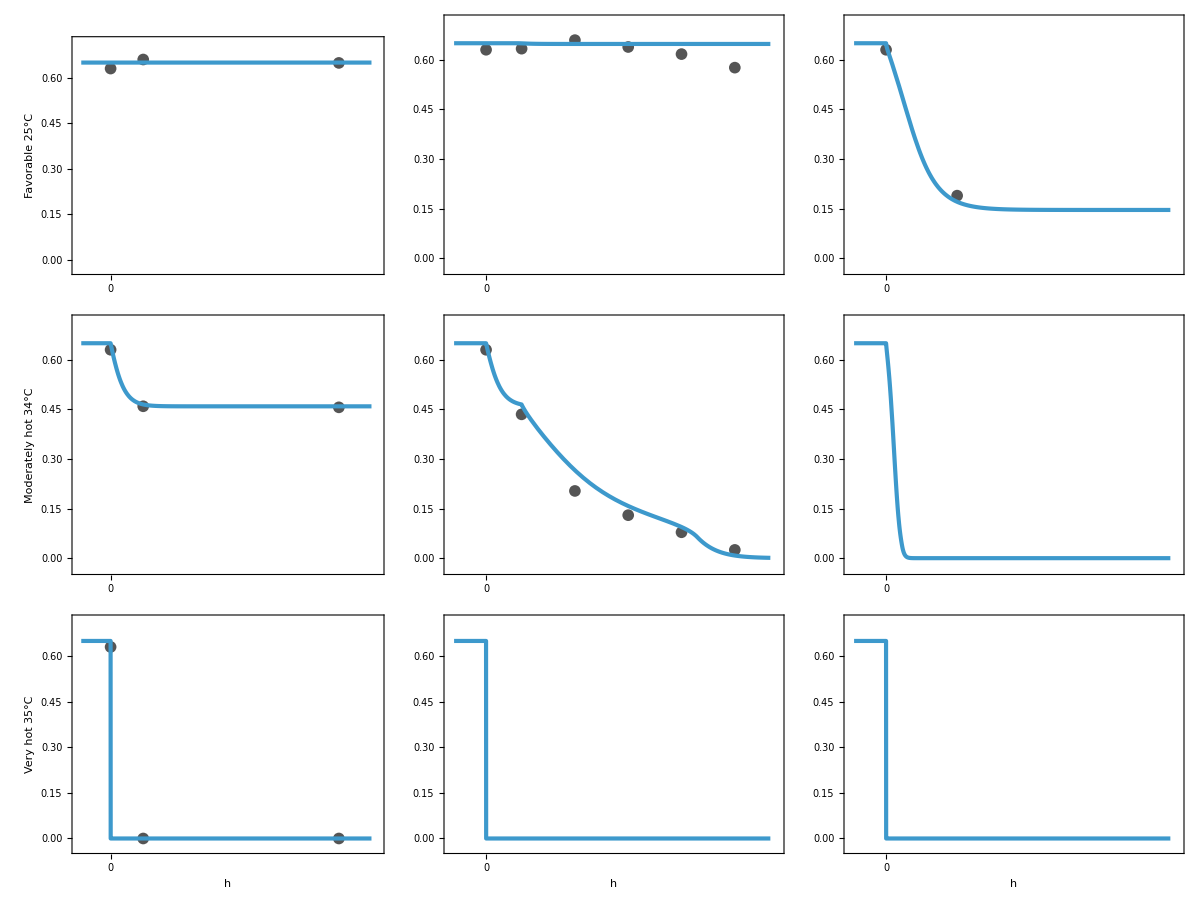
-Graphics-      Temperature      Light

```mathematica
plotSimulationFvFm[pars_,options_:{}]:=plotSimulation[FvFm,pars,{- 0.45 3600,4 3600},
{Evaluate@options,PlotStyle->({thickness,colorCurves}),FrameTicks->{{autoTicks,None},{{0}~Join~hourTicks,None}},PlotRange->{Full,{FvFmMinPlot,FvFmMaxPlot}},Evaluate@style}];
simuPlotPars["MixStress"][parameters_][temperature_,0]:=Join[{
L->Piecewise[{
{40,t<0 3600},
{0,True}
}],
w->Piecewise[{
{25,t<0 3600},
{temperature,True}
}],
tmin->-24 3600,
tmax->24 3600
},
(*pars[4]*)parameters
];
(*plotSimulationFvFm[simuPlotPars["MixStress"][#,0]]&/@tempSelection*)
simuPlotPars["MixStress"][parameters_][temperature_,200]:=Join[{
L->Piecewise[{
{40,t<0 3600},
{0,t<1/2 3600},
{200,True}
}],
w->Piecewise[{
{25,t<0 3600},
{temperature,True}
}],
tmin->-24 3600,
tmax->24 3600
},
(*pars[4]*)parameters
];
(*plotSimulationFvFm[simuPlotPars["MixStress"][#,200]]&/@tempSelection*)
simuPlotPars["MixStress"][parameters_][temperature_,2000]:=Join[{
L->Piecewise[{
{40,t<0 3600},
{2000,True}
}],
w->Piecewise[{
{25,t<0 3600},
{temperature,True}
}],
tmin->-24 3600,
tmax->24 3600
},
(*pars[4]*)parameters
];
(*plotSimulationFvFm[simuPlotPars["MixStress"][25,0]]*)
plotSimulationDataFvFm["MixStress"][parameters_][temperature_,light_,options_:{}]:=Show[{dataPlot["MixStress"][temperature,light,{PlotRangeClipping->False}],plotSimulationFvFm[simuPlotPars["MixStress"][parameters][temperature,light],{PlotRangeClipping->True,PlotRange->{{-.5,4.1}3600,{FvFmMinPlot,FvFmMaxPlot}}}]},Evaluate@options,imageSizePadding[ImagePaddingLeftTop],PlotRange->{{-.5,4.1}3600,{FvFmMinPlot,FvFmMaxPlot}}];


ImagePaddingMinimal={{1,1},{1,1}};
spaceLeftLabel={{65,0},{0,0}};
spaceBottomTickLabel={{0,0},{35,0}};
spaceTopLabel={{0,0},{0,45}};
{tempColors,lightColors}=Table[Table[selection[[i]]->ColorData["Rainbow"][.3+.7 i/3],{i,Length@selection}],{selection,{tempSelection,lightsSelection}}];
lightNames={lightsSelection[[1]]->"Dark",lightsSelection[[2]]->"Intermediate",lightsSelection[[3]]->"High"};
temperatureNames={tempSelection[[1]]->"Favorable",tempSelection[[2]]->"Moderately hot",tempSelection[[3]]->"Very hot"};
optionsMixGrid[light_,temperature_]:={
Frame->True,
FrameStyle->{{Automatic,Directive[White]},{Automatic,Directive[White,FontColor->Darker@Gray]}},
imageSizePadding[ImagePaddingMinimal+Piecewise[{{spaceLeftLabel, light==lightsSelection[[1]]}, {{{0,0},{0,0}}, True}}]+Piecewise[{{spaceTopLabel, temperature==tempSelection[[1]]}, {{{0,0},{0,0}}, True}}]+Piecewise[{{spaceBottomTickLabel, temperature==tempSelection[[3]]}, {{{0,0},{0,0}}, True}}]],
FrameTicks->{{autoTicks,None},{{0}~Join~hourTicks,None}},
(*FrameTicks->{{Piecewise[{{autoTicks, light==lightsSelection[[1]]}, {None, True}}],None},{Piecewise[{{{0}~Join~hourTicks, temperature==tempSelection[[3]]}, {None, True}}],None}},*)
FrameLabel->{
{
Piecewise[{{Style[Column[{temperature/.temperatureNames,Row[{temperature,w/.units}," "]},Alignment->Center],temperature/.tempColors,14], light==lightsSelection[[1]]}, {None, True}}],
None
},
{
Piecewise[{{"h", temperature==tempSelection[[3]]}, {None, True}}],
Piecewise[{{Style[Column[{light/.lightNames,Row[{light,L/.units}," "]},Alignment->Center],light/.lightColors,14], temperature==tempSelection[[1]]}, {None, True}}]
}
},
Piecewise[{{Epilog->Inset[Style["F_V/F_M",14,FontFamily->font],{-.9 3600,0.82}], light==lightsSelection[[1]]∧temperature==tempSelection[[1]]}, {Nothing, True}}]
};
gridPlotSimuDataFvFm[parameters_]:=Labeled[Grid[Table[plotSimulationDataFvFm["MixStress"][parameters][temperature,light,
optionsMixGrid[light,temperature]
] ,{temperature,tempSelection},{light,lightsSelection}]
,Spacings->{1.5,1}],{Style[Rotate[Row[{"Temperature"(*,w/.units*)},"   "],π/2],FontFamily->font,18],Style[Row[{"Light"(*,L/.units*)},"   "],FontFamily->font,17]},{Left,Top}];
(Export[NotebookDirectory[]<>"export/simulations-temp-light-grid.pdf",#];#)&@gridPlotSimuDataFvFm[pars[4]]
```

```mathematica
Table[Export[NotebookDirectory[]<>"export/"<>figureDirectoryGrid<>"/"<>figureNameGrid<>"-temperature="<>ToString[temperature]<>"-light="<>ToString[light]<>".pdf",#]&@fullSimulationPanel[simuPlotPars["MixStress"][pars[4]][temperature,light],{- 0.45 3600,4 3600},{FrameTicks->{{autoTicks,None},{{0}~Join~hourTicks,None}}},{(FrameLabel->{{#/.units,None},{"h",None}})}&], {temperature,tempSelection},{light,lightsSelection}];
```

```mathematica
figureDirectoryGridAlternativeParameters="light_temperature_grid_alternative_parameters";
```

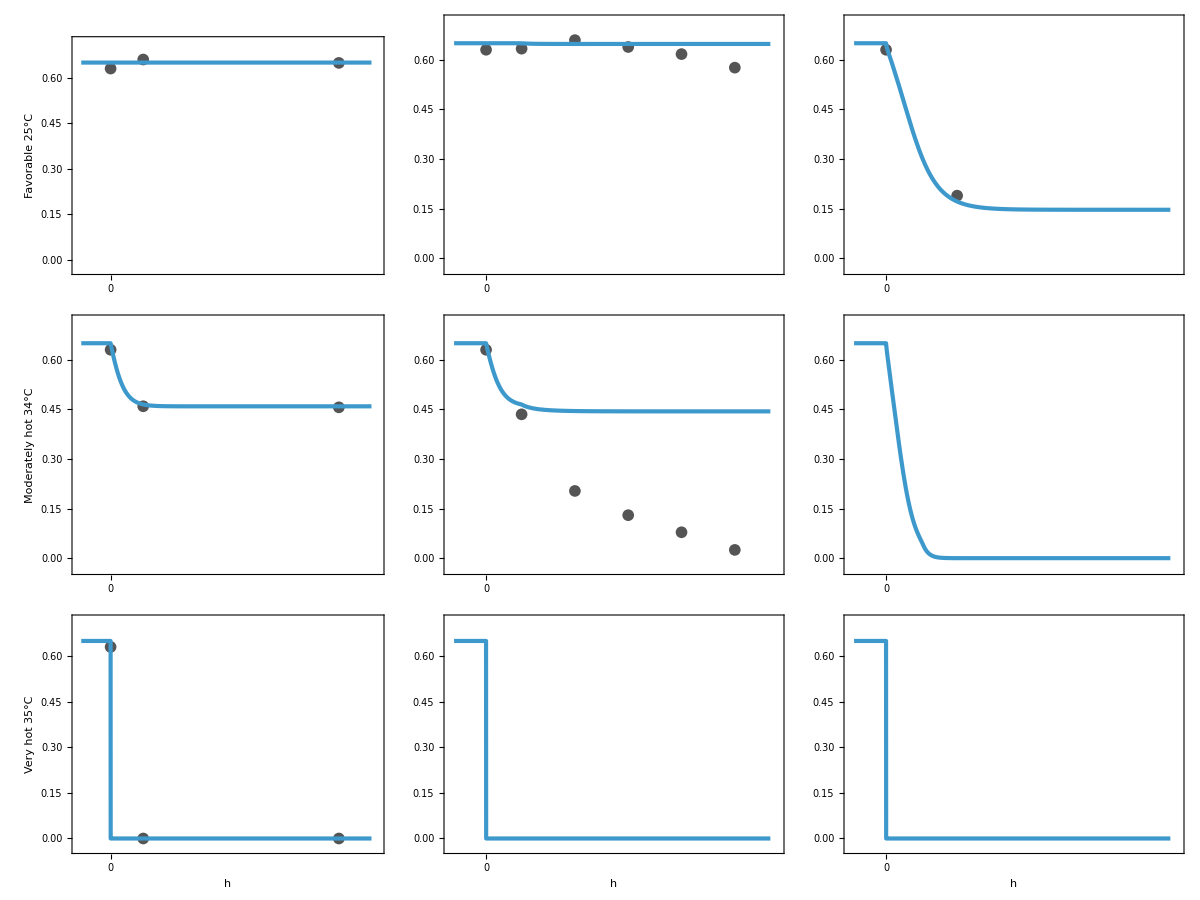
-Graphics-      Temperature      Light

```mathematica
parsSameDamageLow={
ϕDpX->28,
ϕDpD->28,
ϕDpT->28
};
(Export[NotebookDirectory[]<>"export/"<>figureDirectoryGridAlternativeParameters<>"/"<>"simulations-temp-light-grid-all-p-same-damage-low-damage.pdf",#];#)&@gridPlotSimuDataFvFm[Join[parsSameDamageLow,pars[4]]]
```

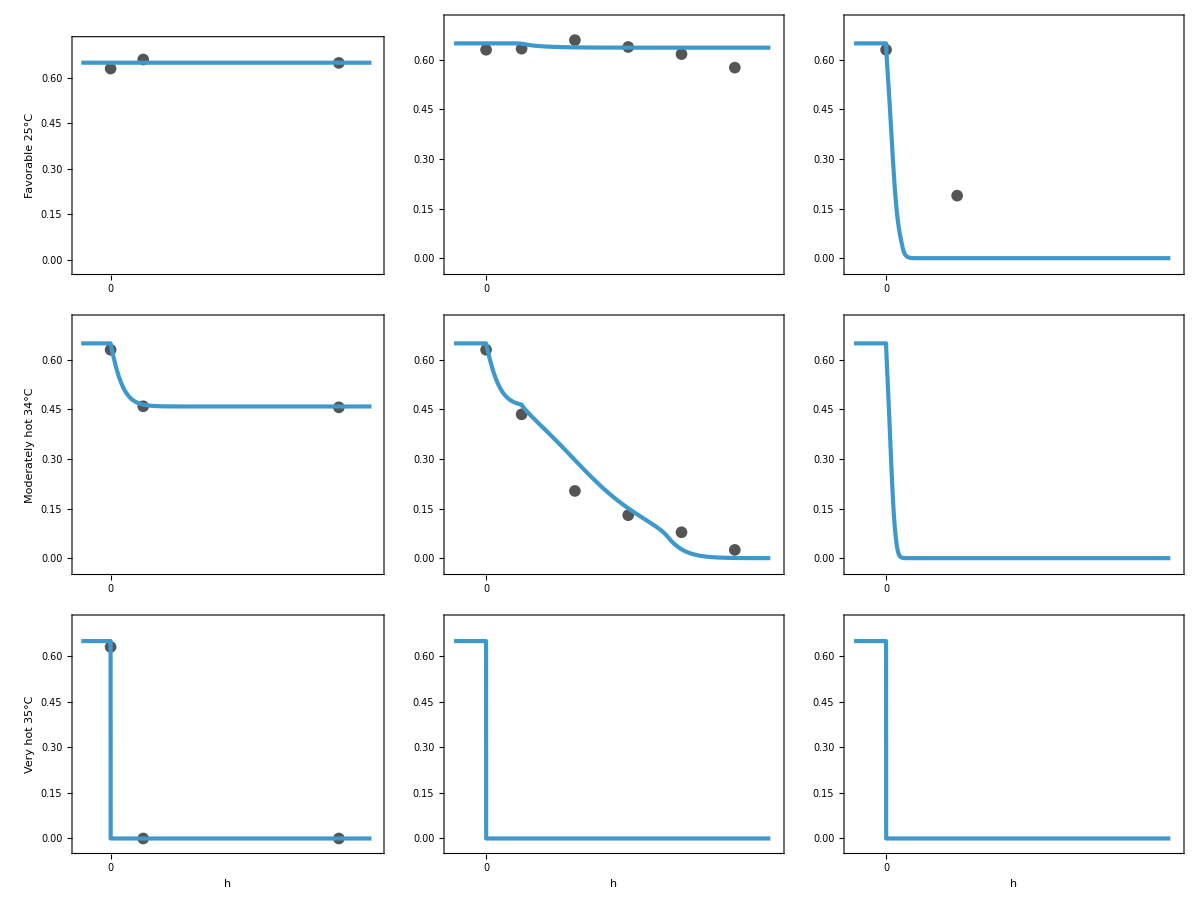
-Graphics-      Temperature      Light

```mathematica
parsSameDamageHigh={
ϕDpX->100,
ϕDpD->100,
ϕDpT->100
};
(Export[NotebookDirectory[]<>"export/"<>figureDirectoryGridAlternativeParameters<>"/"<>"simulations-temp-light-grid-all-p-same-damage-high-damage.pdf",#];#)&@gridPlotSimuDataFvFm[Join[parsSameDamageHigh,pars[4]]]
```

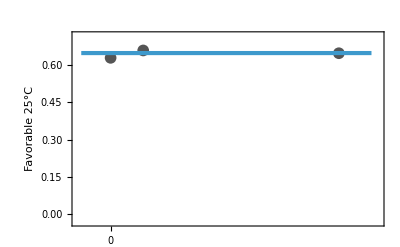
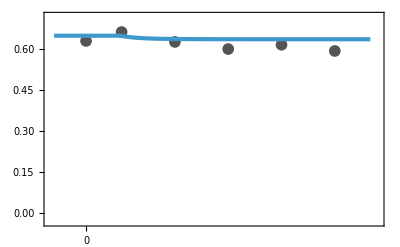
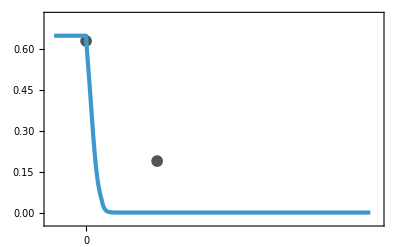
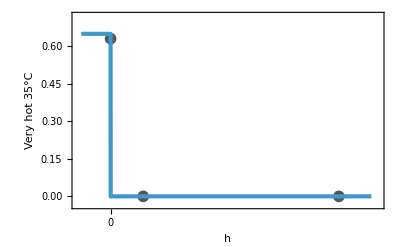
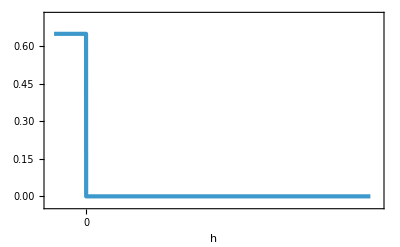
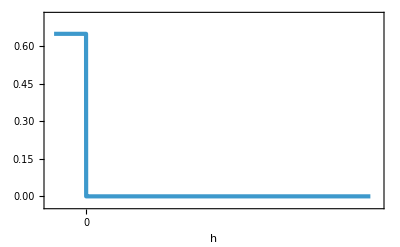
```mathematica
{{-Graphics-, -Graphics-, -Graphics-}, {, □, □}, {-Graphics-, -Graphics-, -Graphics-}}   "   ""Temperature"   "   ""Light"
```

-Graphics- | -Graphics- | -Graphics-
 | □ | □
-Graphics- | -Graphics- | -Graphics-      Temperature      Light

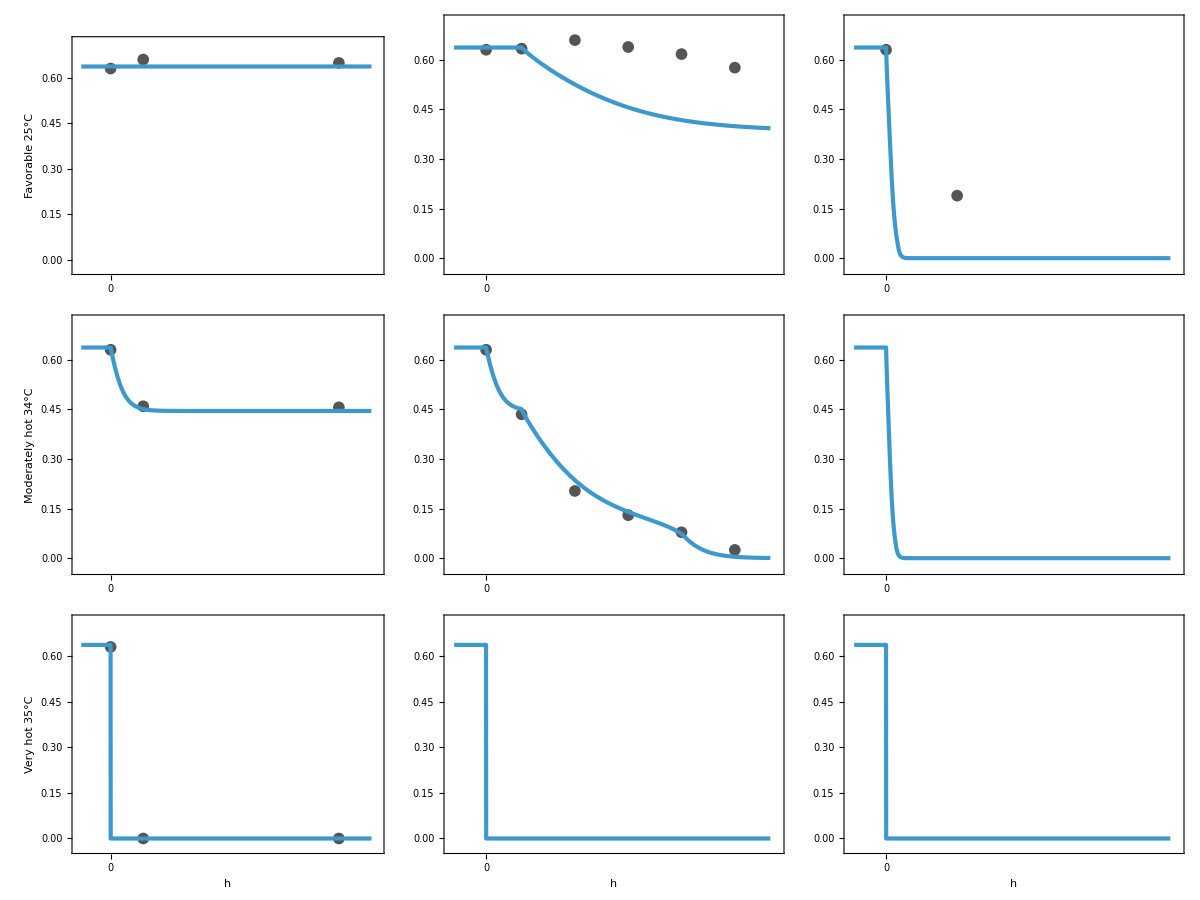
-Graphics-      Temperature      Light

```mathematica
figureDirectoryGridAlternativeParametersChlROS="light_temperature_grid_alternative_ROS_from_chl";
parsChlDamageHighDamage={
ϕDpX->0,
ϕDpD->0,
ϕDpT->0,
ϕDcX->10^3.5
};

(Export[NotebookDirectory[]<>"export/"<>figureDirectoryGridAlternativeParametersChlROS<>"/"<>"simulations-temp-light-grid-ROS-from-chl-high-damage.pdf",#];#)&@Quiet@gridPlotSimuDataFvFm[Join[parsChlDamageHighDamage,pars[4]]]
```

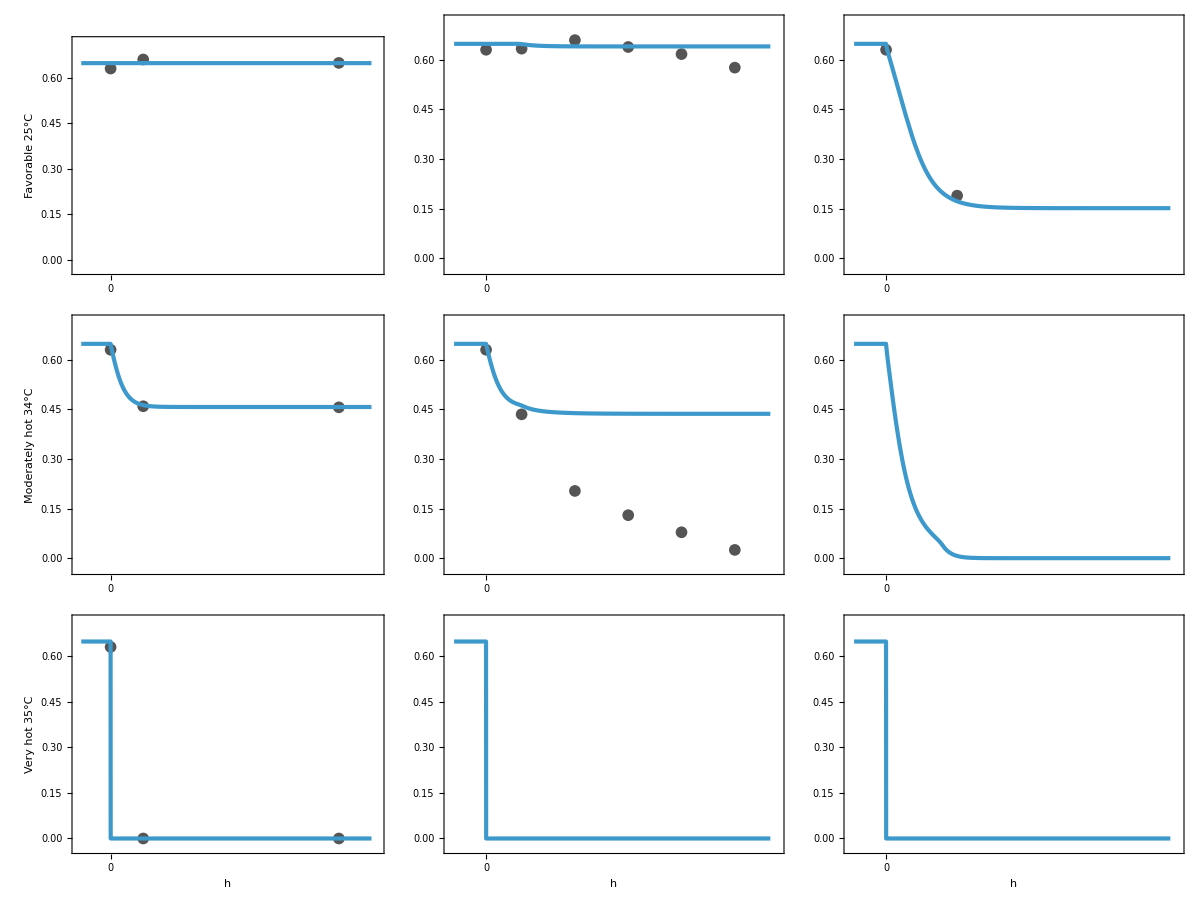
-Graphics-      Temperature      Light

```mathematica
parsChlDamageLowDamage={
ϕDpX->0,
ϕDpD->0,
ϕDpT->0,
ϕDcX->10^2.85
};

(Export[NotebookDirectory[]<>"export/"<>figureDirectoryGridAlternativeParametersChlROS<>"/"<>"simulations-temp-light-grid-ROS-from-chl-low-damage.pdf",#];#)&@Quiet@gridPlotSimuDataFvFm[Join[parsChlDamageLowDamage,pars[4]]]
```